```mathematica
Clear["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks

```mathematica
$ProcessorCount
```

14

## Filter Scheme

P ϕ'=1/h Q (𝕀+σ R^-1 S)ϕ

### Interior

β Δ̂ f_(i-2)+α Δ̂ f_(i-1)+Δ̂ f_i+α Δ̂ f_(i+1)+β Δ̂ f_(i+2)=∑_(m=1)^(n/2) a_m(f_(i-m)-2 f_i+f_(i+m))
Use Taylor series to determine constraint equations for a_m

T(κ)=1+(2∑_(m=1)^(n/2) a_m[cos(m κ)-1])/(1+2α cos(κ) + 2β cos(2κ))

```mathematica
InteriorKimSpectral[order_,κ_,aList_]:=1+(2Sum[aList[[m]](Cos[m κ]-1),{m,1,order/2}])/(1+2α Cos[κ]+2β Cos[2κ])
```

```mathematica
KimFilterInterior[order_]:=Module[{aList,n,system,coeffs},
n=order/2;
aList=Table[Symbol["a"<>ToString[i]],{i,1,n}];
coeffs=Flatten[Append[aList,{α,β}]];
system={};
AppendTo[system,InteriorKimSpectral[order,κc,aList]==1/2];
Do[
AppendTo[system,Sum[j^i aList[[j]],{j,1,n}]==0]
,{i,2,order-1,2}];

AppendTo[system,InteriorKimSpectral[order,π,aList]==0];
AppendTo[system,(D[InteriorKimSpectral[order,κ,aList],{κ,2}]/.κ->π)==0];
system=system//Simplify;
(*Print[system];*)

Solve[system,coeffs]
]
interiorCoeffs=KimFilterInterior[6][[1]]//FullSimplify
```

{a1→-(30 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a2→(12 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a3→-(2 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),α→(4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),β→1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])}

### Boundary

#### Polynomial Generator

```mathematica
(*κc=0.7π;
ϵ=0.09*)

(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=2; (*number of free parameters used for Kim's optimization on the interior*)
(*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}]
numBoundaryRows=Length@RHSPars
fOrder=4;
dhatfOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+dhatfOrder-1;


rowf1=Join[{1},Table[0,{i,1,fOrder}]];
rowf=Table[Table[i^j,{j,0,fOrder}],{i,1,fOrder}];
rowdhatf1=Join[{1},Table[0,{i,1,fOrder}]];
rowdhatf=Table[Table[i^j,{j,0,fOrder}],{i,1,fOrder}];
rowdhatfb ={{6-a1-a2-a3, -6+2a1+3a2+4a3,6-4a1-9a2-16a3, -6+8a1+27a2+64a3,6-16a1-81a2-256a3,1+α+β,-1-2α-3β,1+4α+0β,-1-8α-27β, 1+16α+81β},{4-a2-a3,-8+4a2+5a3,16-16a2-25a3,-32+64a2+123a3,64-256a2-625a3,1+2α+β,-2-4α-4β,4+10α+16β,-8-28α-64β,16+82α+256β}} ;

matf=PrependTo[rowf,rowf1];
matdhatf=PrependTo[rowdhatf,rowdhatf1];
LMat=BlockDiagonalMatrix[{matf,matdhatf}];
LMat[[9]]=rowdhatfb[[1]];
LMat[[10]]=rowdhatfb[[2]];

RMat = IdentityMatrix[10];
RMat[[9]] = {a1, a2, a3, 0, 0, -α, -β, 0, 0, 0};
RMat[[10]] = {a2, a3, 0, 0, 0, -β, 0, 0,0, 0};

cVec=Table[ToExpression[StringJoin["c",ToString[i]]],{i,0,fOrder}];
dVec=Table[ToExpression[StringJoin["d",ToString[i]]],{i,0,fOrder}];
pVec = Join[cVec, dVec];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder}],Table[ToExpression[StringJoin["dhatf",ToString[i]]],{i,0,fOrder}]];

pCoeffs=Solve[LMat.pVec==RMat. fVec,pVec][[1]]//FullSimplify;

g[x_]=Total[Table[cVec[[i+1]]*x^i,{i,0,fOrder}]]/.pCoeffs;
dhatg[x_]=Total[Table[dVec[[i+1]]*x^i,{i,0,fOrder}]]/.pCoeffs;

(*other info to print?*)
Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[RMat]," ",MatrixForm[fVec]]
Print["Coefficients:\n",MatrixForm[pCoeffs]]
```

{a1,a2,a3}

3

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 2 | 4 | 8 | 16 | 0 | 0 | 0 | 0 | 0
1 | 3 | 9 | 27 | 81 | 0 | 0 | 0 | 0 | 0
1 | 4 | 16 | 64 | 256 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 2 | 4 | 8 | 16
6-a1-a2-a3 | -6+2 a1+3 a2+4 a3 | 6-4 a1-9 a2-16 a3 | -6+8 a1+27 a2+64 a3 | 6-16 a1-81 a2-256 a3 | 1+α+β | -1-2 α-3 β | 1+4 α | -1-8 α-27 β | 1+16 α+81 β
4-a2-a3 | -8+4 a2+5 a3 | 16-16 a2-25 a3 | -32+64 a2+123 a3 | 64-256 a2-625 a3 | 1+2 α+β | -2-4 α-4 β | 4+10 α+16 β | -8-28 α-64 β | 16+82 α+256 β) (c0
c1
c2
c3
c4
d0
d1
d2
d3
d4) = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
a1 | a2 | a3 | 0 | 0 | -α | -β | 0 | 0 | 0
a2 | a3 | 0 | 0 | 0 | -β | 0 | 0 | 0 | 0) (f0
f1
f2
f3
f4
dhatf0
dhatf1
dhatf2
dhatf3
dhatf4)

Coefficients:
(c0→f0
c1→-(25 f0)/12+4 f1-3 f2+(4 f3)/3-f4/4
c2→1/24 (35 f0-104 f1+114 f2-56 f3+11 f4)
c3→1/12 (-5 f0+18 f1-24 f2+14 f3-3 f4)
c4→1/24 (f0-4 f1+6 f2-4 f3+f4)
d0→dhatf0
d1→(-4 α ((-1350+1488 a1+1551 a2+3506 a3) f0-12 (-145+310 a1+358 a2+904 a3) f1-1260 f2+4185 a1 f2+4998 a2 f2+13269 a3 f2+486 f3-2232 a1 f3-2670 a2 f3-7376 a3 f3-78 f4+465 a1 f4+555 a2 f4+1587 a3 f4+147 dhatf0 α+3 dhatf2 (6+17 α))-2 (6 dhatf2+(-1080+768 a1+1254 a2+2609 a3) f0-192 (-10+10 a1+19 a2+43 a3) f1+24 (-75+90 a1+182 a2+428 a3) f2-4 (288 a1+600 a2+1451 a3) f3+3 (80 a1+170 a2+421 a3) f4+12 (72 f3-14 f4+dhatf0 α))-3 (2 ((-1560+2560 a1+1766 a2+4441 a3) f0-64 (-15+100 a1+71 a2+209 a3) f1+8 (15+900 a1+630 a2+2002 a3) f2-4 (96+960 a1+640 a2+2179 a3) f3+(120+800 a1+510 a2+1847 a3) f4)-31 dhatf0 (16+13 α)+dhatf2 (-28+131 α)) β+5496 dhatf0 β^2+12 dhatf1 (8+α (45+112 α)-64 β+84 α β-352 β^2))/(18 (8+8 α (5+9 α)-8 β+67 α β-200 β^2))
d2→(-6 dhatf2+(-2520+1536 a1+2934 a2+5969 a3) f0+24 (-8 (-25+20 a1+45 a2+99 a3) f1+(-195+180 a1+434 a2+990 a3) f2)-4 (288 (-2+2 a1+5 a2)+3371 a3) f3+3 (-152+160 a1+410 a2+981 a3) f4-6 dhatf0 (30+181 α^2+8 β (33+35 β)+4 α (39+131 β))+2 (α ((-3510+3408 a1+4047 a2+8902 a3) f0-12 (-425+710 a1+950 a2+2312 a3) f1-4140 f2+9585 a1 f2+13398 a2 f2+34125 a3 f2+1782 f3-5112 a1 f3-7230 a2 f3-19072 a3 f3+3 (-106+355 a1+505 a2+1373 a3) f4+3 dhatf2 (-4+7 α))+(5 ((-1080+1920 a1+1218 a2+3143 a3) f0-96 (-5+50 a1+32 a2+98 a3) f1+24 (15+225 a1+140 a2+467 a3) f2-4 (108+720 a1+420 a2+1517 a3) f3+3 (40+200 a1+110 a2+427 a3) f4)+12 dhatf2 (-4+11 α)) β+300 dhatf2 β^2+3 dhatf1 (16+64 α^2+40 (3-2 β) β+5 α (15+22 β))))/(18 (8+8 α (5+9 α)-8 β+67 α β-200 β^2))
d3→(8 (-6 dhatf1+(-45 dhatf1+18 dhatf2+(270+48 a1-321 a2-541 a3) f0-12 (65+10 a1-86 a2-152 a3) f1+900 f2+135 a1 f2-1302 a2 f2-2373 a3 f2-486 f3-72 a1 f3+750 a2 f3+1396 a3 f3+3 (34+5 a1-55 a2-104 a3) f4) α+3 (19 dhatf0-28 dhatf1+11 dhatf2) α^2)+4 (6 dhatf2+a3 (89 f0-192 f1+156 f2-44 f3+3 f4)+12 a1 (16 f0-40 f1+45 f2-24 f3+5 f4)-6 a2 (f0-16 f1+28 f2-20 f3+5 f4)+24 (-10 f1+15 f2-9 f3+2 f4+2 dhatf0 α))+3 (10 dhatf2-(120+1280 a1-182 a2+343 a3) f0+64 (30+50 a1-17 a2+7 a3) f1-8 (345+450 a1-210 a2-4 a3) f2+4 (408+480 a1-280 a2-83 a3) f3+(-360-400 a1+270 a2+119 a3) f4+94 dhatf2 α-4 dhatf1 (4+57 α)+dhatf0 (28+226 α)) β-12 (58 dhatf0-152 dhatf1+75 dhatf2) β^2)/(36 (8+8 α (5+9 α)-8 β+67 α β-200 β^2))
d4→-(-12 dhatf2+2 (-360+384 a1+414 a2+929 a3) f0-8 (24 (-5+10 a1+12 a2+30 a3) f1-6 (-15+45 a1+56 a2+147 a3) f2+36 (-1+4 a1+5 a2) f3+491 a3 f3)+6 (-8+40 a1+50 a2+141 a3) f4+4 (-12 dhatf2+(-270+528 a1+303 a2+808 a3) f0-12 (-5+110 a1+62 a2+200 a3) f1+180 f2+1485 a1 f2+798 a2 f2+2841 a3 f2-162 f3-792 a1 f3-390 a2 f3-1528 a3 f3+3 (14+55 a1+25 a2+107 a3) f4) α-60 dhatf2 α^2+((-3240+3840 a1+3714 a2+8539 a3) f0+24 (-8 (-20+50 a1+53 a2+137 a3) f1+(-105+450 a1+490 a2+1336 a3) f2)-4 (24 (-9+60 a1+65 a2)+4441 a3) f3+3 (-40+400 a1+430 a2+1271 a3) f4+6 dhatf2 (1+4 α)) β+300 dhatf2 β^2+12 dhatf1 (4+16 α^2+4 (3-8 β) β+5 α (3+4 β))-12 dhatf0 (6+25 α^2+11 β (3+2 β)+α (24+65 β)))/(36 (8+8 α (5+9 α)-8 β+67 α β-200 β^2)))

#### Node 2

```mathematica
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]

scheme0=β dhatf0+α dhatf1+dhatf2+α dhatf3+β dhatf4-(a3 g[-1]+a2 f0+a1 f1-2(a1+a2+a3)f2+a1 f3+a2 f4+a3 f5);(*==0*)
schemedhatf5=Solve[β dhatf1+α dhatf2+dhatf3+α dhatf4+β dhatf5==+a3 f0+a2 f1+a1 f2-2(a1+a2+a3)f3+a1 f4+a2 f5+a3 f6,dhatf5][[1]];
scheme0=scheme0/.schemedhatf5//FullSimplify;
schemebd=γ20 dhatf0+γ21 dhatf1+γ22 dhatf2+γ23 dhatf3+γ24 dhatf4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)

fVars2={dhatf0,dhatf1,dhatf2,dhatf3,dhatf4,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd;(*==0*)
eq=Collect[eq,fVars2];

coeffEqs2={};
For[i=1,i<=Length[fVars2],i++,
AppendTo[coeffEqs2,Coefficient[eq,fVars2[[i]]]==0]]

bdCoeffs2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};


coeffEqs2;

bdCoeffs2=Solve[coeffEqs2,bdCoeffs2][[1]]/.interiorCoeffs;
coeffs2={γ22->(γ22/γ22/.bdCoeffs2),
γ20->(γ20/γ22/.bdCoeffs2),
γ21->(γ21/γ22/.bdCoeffs2),
γ23->(γ23/γ22/.bdCoeffs2),
γ24->(γ24/γ22/.bdCoeffs2),
a20->(a20/γ22/.bdCoeffs2),
a21->(a21/γ22/.bdCoeffs2),
a22->(a22/γ22/.bdCoeffs2),
a23->(a23/γ22/.bdCoeffs2),
a24->(a24/γ22/.bdCoeffs2),
a25->(a25/γ22/.bdCoeffs2),
a26->(a26/γ22/.bdCoeffs2)}
```

{γ22→1,γ20→1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]),γ21→(4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),γ23→(4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),γ24→1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]),a20→(2 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a21→-(10 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a22→(20 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a23→-(20 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a24→(10 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a25→-(2 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]),a26→0}

#### Node 1

```mathematica
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]

scheme0=β dhatg[-1]+α dhatf0+dhatf1+α dhatf2+β dhatf3-(a3 g[-2]+a2 g[-1]+a1 f0-2(a1+a2+a3)f1 +a1 f2+a2 f3+a3 f4); (*==0*)
schemedhatf5=Solve[β dhatf1+α dhatf2+dhatf3+α dhatf4+β dhatf5==+a3 f0+a2 f1+a1 f2-2(a1+a2+a3)f3+a1 f4+a2 f5+a3 f6,dhatf5][[1]];
schemedhatf4=Solve[γ20 dhatf0+γ21 dhatf1+γ22 dhatf2+γ23 dhatf3+γ24 dhatf4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6,dhatf4][[1]];
scheme0=scheme0/.schemedhatf5;
scheme0=scheme0/.schemedhatf4/.coeffs2;
schemebd=γ10 dhatf0+γ11 dhatf1+γ12 dhatf2+γ13 dhatf3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)

fVars1={dhatf0,dhatf1,dhatf2,dhatf3,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars1];

coeffEqs1={};
For[i=1,i<=Length[fVars1],i++,
AppendTo[coeffEqs1,Coefficient[eq,fVars1[[i]]]==0]]

bdCoeffs1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};

coeffEqs1;

bdCoeffs1=Solve[coeffEqs1,bdCoeffs1][[1]]/.interiorCoeffs;

coeffs1={γ11->(γ11/γ11/.bdCoeffs1),
γ10->(γ10/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
γ12->(γ12/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
γ13->(γ13/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a10->(a10/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a11->(a11/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a12->(a12/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a13->(a13/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a14->(a14/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a15->(a15/γ11/.bdCoeffs1)(*/.int/.κc->(1-2ϵ)κc*),
a16->(a16/γ11/.bdCoeffs1)}
```

{γ11→1,γ10→(1/6+(4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])+(320 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(16 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((-28-(904 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(12 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(31 (16+(52 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(6 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(286 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)+((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (6+(400 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+11 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3+2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(4 Cos[κc] (7+Cos[2 κc]) (24+65 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (30+(2896 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (33+35 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(16 Cos[κc] (7+Cos[2 κc]) (39+131 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)))/(1+(4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(896 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(40 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((4+(228 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(152 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (8+(4 Cos[κc] (7+Cos[2 κc]) (45+(448 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-64 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(336 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-352 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (4+(256 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (3+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (16+(1024 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+40 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (15+22 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))),γ12→((4 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-(272 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(32 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(4 Cos[κc] (7+Cos[2 κc]) (-4+(28 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(8 Cos[κc] (7+Cos[2 κc]) (6+(68 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(5 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(6 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(94 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((-1-(16 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(6 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(4 (-4+(44 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((-28+(524 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(6 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(50 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))/(1+(4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(896 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(40 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((4+(228 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(152 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (8+(4 Cos[κc] (7+Cos[2 κc]) (45+(448 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-64 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(336 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-352 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (4+(256 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (3+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (16+(1024 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+40 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (15+22 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))),γ13→(1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))/(1+(4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(896 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(40 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((4+(228 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(152 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (8+(4 Cos[κc] (7+Cos[2 κc]) (45+(448 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-64 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(336 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-352 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (4+(256 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (3+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (16+(1024 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+40 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (15+22 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))),a10→(-((6010 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(9 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)))-(4 Cos[κc] (7+Cos[2 κc]) (-3510-(71480 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(9 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(8 Cos[κc] (7+Cos[2 κc]) (-1350-(33040 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(9 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((-2520-(22810 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(18 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((-1080-(13210 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(9 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(8 Cos[κc] (7+Cos[2 κc]) (270-(4210 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(9 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((360+(8410 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(18 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(4 Cos[κc] (7+Cos[2 κc]) (270+(13820 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(9 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((-1560-(64490 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(5 (-1080-(49270 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(9 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((120-(41270 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(12 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((3240+(87710 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(36 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)))/(1+(4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(896 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(40 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((4+(228 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(152 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (8+(4 Cos[κc] (7+Cos[2 κc]) (45+(448 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-64 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(336 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-352 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (4+(256 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (3+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (16+(1024 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+40 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (15+22 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))),a11→(-(80 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(5312 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(16 Cos[κc] (7+Cos[2 κc]) (-425-(14524 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(32 Cos[κc] (7+Cos[2 κc]) (-145-(6812 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(16 Cos[κc] (7+Cos[2 κc]) (-5-(2956 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(32 Cos[κc] (7+Cos[2 κc]) (65-(1028 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(32 (-25-(258 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(16 (-5-(216 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(64 (-10-(158 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(64 (-15-(2566 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(16 (30-(1718 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(160 (-5-(1312 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(16 (-20-(1138 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)))/(1+(4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(896 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(40 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((4+(228 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(152 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (8+(4 Cos[κc] (7+Cos[2 κc]) (45+(448 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-64 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(336 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-352 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (4+(256 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (3+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (16+(1024 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+40 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (15+22 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))),a12→((40 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)+(137216 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(6176 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(3840 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(4 (-195-(2172 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(8 (-75-(1372 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(4 (-15-(972 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(8 (15-(23444 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(2 (345-(16012 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(2 (-105-(10292 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(40 (15-(6004 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)))/(1+(4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(896 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(40 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((4+(228 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(152 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (8+(4 Cos[κc] (7+Cos[2 κc]) (45+(448 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-64 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(336 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-352 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (4+(256 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (3+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (16+(1024 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+40 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (15+22 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))),a13→(-(120 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)-(220288 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(5236 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(9 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(1728 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(2 (-576-(6742 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(9 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(8 (-1-(60 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)+(4 (96-(25478 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(20 (108-(19594 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(9 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((-408+(17594 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2 (-(8882 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])+24 (-9-(1020 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]))))/(9 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)))/(1+(4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(896 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(40 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((4+(228 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(152 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (8+(4 Cos[κc] (7+Cos[2 κc]) (45+(448 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-64 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(336 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-352 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (4+(256 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (3+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (16+(1024 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+40 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (15+22 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))),a14→((24 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)+(27904 Cos[κc/2]^4 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(160 Cos[κc/2]^4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(208 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(4 Cos[κc] (7+Cos[2 κc]) (-106-(7336 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((-152-(1842 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(6 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(8 Cos[κc] (7+Cos[2 κc]) (34-(602 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((8+(882 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(6 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(4 Cos[κc] (7+Cos[2 κc]) (-14+(1564 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((120-(21574 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((360-(15002 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(12 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(5 (40-(5534 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((40+(9382 Cos[κc/2]^4)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(12 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)))/(1+(4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(896 Cos[κc]^2 (7+Cos[2 κc])^2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(3 (5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+(40 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/((5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc]) (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((4+(228 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(152 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^3)/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-(2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (8+(4 Cos[κc] (7+Cos[2 κc]) (45+(448 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-64 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(336 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-352 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))-((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (4+(256 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (3+4 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))+((1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (16+(1024 Cos[κc]^2 (7+Cos[2 κc])^2)/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])^2+40 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])) (3-2 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))+(20 Cos[κc] (7+Cos[2 κc]) (15+22 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(3 (8+(32 Cos[κc] (7+Cos[2 κc]) (5+(36 Cos[κc] (7+Cos[2 κc]))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-8 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))+(268 Cos[κc] (7+Cos[2 κc]) (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc])))/(5 Cos[κc]-10 (3+Cos[2 κc])+3 Cos[3 κc])-200 (1/6-(32 Cos[κc/2]^4)/(15 Cos[κc]-30 (3+Cos[2 κc])+9 Cos[3 κc]))^2))),a15→0,a16→0}

#### Node 0

```mathematica
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

scheme0=β dhatg[-2]+α dhatg[-1]+dhatf0+α dhatf1+β dhatf2-(a3 g[-3]+a2 g[-2]+a1 g[-1]-2(a1+a2+a3)f0+a1 f1+a2 f2+a3 f3); (*==0*)
schemedhatf5=Solve[β dhatf1+α dhatf2+dhatf3+α dhatf4+β dhatf5==a3 f0+a2 f1+a1 f2-2(a1+a2+a3)f3+a1 f4+a2 f5+a3 f6,dhatf5][[1]];
schemedhatf4=Solve[γ20 dhatf0+γ21 dhatf1+γ22 dhatf2+γ23 dhatf3+γ24 dhatf4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6,dhatf4][[1]];
schemedhatf3=Solve[γ10 dhatf0+γ11 dhatf1+γ12 dhatf2+γ13 dhatf3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6,dhatf3][[1]];
scheme0=scheme0/.schemedhatf5;
scheme0=scheme0/.schemedhatf4/.coeffs2;
scheme0=scheme0/.schemedhatf3/.coeffs1;
schemebd=γ00 dhatf0+γ01 dhatf1+γ02 dhatf2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)

fVars0={dhatf0,dhatf1,dhatf2,f0,f1,f2,f3,f4,f5,f6};
eq=scheme0-schemebd; (*==0*)
eq=Collect[eq,fVars0];

coeffEqs0={};
For[i=1,i<=Length[fVars0],i++,
AppendTo[coeffEqs0,Coefficient[eq,fVars0[[i]]]==0]]

bdCoeffs0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};

coeffEqs0;

bdCoeffs0=Solve[coeffEqs0,bdCoeffs0][[1]]/.interiorCoeffs;

coeffs0={γ00->(γ00/γ00/.bdCoeffs0),
γ01->(γ01/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
γ02->(γ02/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a00->(a00/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a01->(a01/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a02->(a02/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a03->(a03/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a04->(a04/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a05->(a05/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*)),
a06->(a06/γ00/.bdCoeffs0(*/.int/.κc->(1-2ϵ)κc*))}
```

#### Dump Saves

```mathematica
coeffs2 = coeffs2/.κc->(1-1ϵ)κc;
coeffs1 = coeffs1/.κc->(1-2ϵ)κc;
coeffs0 = coeffs0/.κc->(1-3ϵ)κc;

DumpSave["bdCoeffs2.mx","Global`coeffs2"]
DumpSave["bdCoeffs1.mx","Global`coeffs1"]
DumpSave["bdCoeffs0.mx","Global`coeffs0"]
```

{Global`coeffs2}

{Global`coeffs1}

{Global`coeffs0}

### Building the Matrix

#### Full Matrix

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),a00,
If[(i==k&&j==k-1),a01,
If[(i==k&&j==k-2),a02,
If[(i==k&&j==k-3),a03,
If[(i==k&&j==k-4),a04,
If[(i==k&&j==k-5),a05,
If[(i==k&&j==k-6),a06,
If[(i==k-1&&j==k),a10,
If[(i==k-1&&j==k-1),a11,
If[(i==k-1&&j==k-2),a12,
If[(i==k-1&&j==k-3),a13,
If[(i==k-1&&j==k-4),a14,
If[(i==k-1&&j==k-5),a15,
If[(i==k-1&&j==k-6),a16,
If[(i==k-2&&j==k),a20,
If[(i==k-2&&j==k-1),a21,
If[(i==k-2&&j==k-2),a22,
If[(i==k-2&&j==k-3),a23,
If[(i==k-2&&j==k-4),a24,
If[(i==k-2&&j==k-5),a25,
If[(i==k-2&&j==k-6),a26,


If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j, a0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];

LHS[10]//MatrixForm
RHS[10]//MatrixForm
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0
a2 | a1 | a0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
a3 | a2 | a1 | a0 | a1 | a2 | a3 | 0 | 0 | 0
0 | a3 | a2 | a1 | a0 | a1 | a2 | a3 | 0 | 0
0 | 0 | a3 | a2 | a1 | a0 | a1 | a2 | a3 | 0
0 | 0 | 0 | a3 | a2 | a1 | a0 | a1 | a2 | a3
0 | 0 | 0 | a26 | a25 | a24 | a23 | a22 | a21 | a20
0 | 0 | 0 | a16 | a15 | a14 | a13 | a12 | a11 | a10
0 | 0 | 0 | a06 | a05 | a04 | a03 | a02 | a01 | a00)

## Eigenvalue tests

### Kim 2007 Scheme

```mathematica
kimPent6th[n_]:=Module[{P,Q,α,β,a0,a1,a2,a3,γ01,γ02,γ10,γ12,γ13,γ20,γ21,γ23,γ24,γS12,γS13,γS20,γS21,γS23,γS24,b22Filter,b00,b01,b02,b03,b04,b05,b06,b10,b11,b12,b13,b14,b15,b16,b20,b21,b22,b23,b24,b25,b26,bS11,bS12,bS13,bS14,bS15,bS16,bS21,bS22,bS23,bS24,bS25,bS26},
α=0.5862704032801503;
β=0.09549533555017055;
a1=0.6431406736919156;
a2=0.2586011023495066;
a3=0.007140953479797375;

γ01=5.912678614078549;
γ02=3.775623951744012;
γ10=0.08360703307833438;
γ12=2.058102869495757;
γ13=0.9704052014790193;
γ20=0.03250008295108466;
γ21=0.3998040493524358;
γ23=0.7719261277615860;
γ24=0.1626635931256900;

b01=-3.456878182643609;
b02=5.839043358834730;
b03=1.015886726041007;
b04=-0.2246526470654333;
b05=0.08564940889936562;
b06=-0.01836710059356763;
b00=-(b01+b02+b03+b04+b05+b06);

b10=-0.3177447290722621;
b12=-0.02807631929593225;
b13=1.593461635747659;
b14=0.2533027046976367;
b15=-0.03619652460174756;
b16=0.004080281419108407;
b11=-(b10+b12+b13+b14+b15+b16);

b20=-0.1219006056449124;
b21=-0.6301651351188667;
b23=0.6521195063966084;
b24=0.3938843551210350;
b25=0.01904944407973912;
b26=-0.001027260523947668;
b22=-(b20+b21+b23+b24+b25+b26);

γS12=(γ12-γ10 γ02)/(1-γ10 γ01);
γS13=γ13/(1-γ10 γ01);
γS21=(γ10 γ21-γ20)/(γ10-γ20 γ12);
γS23=(γ10 γ23-γ20 γ13)/(γ10-γ20 γ12);
γS24=(γ10 γ24)/(γ10-γ20 γ12);

bS11=(b11-γ10 b01)/(1-γ10 γ01);
bS12=(b12-γ10 b02)/(1-γ10 γ01);
bS13=(b13-γ10 b03)/(1-γ10 γ01);
bS14=(b14-γ10 b04)/(1-γ10 γ01);
bS15=(b15-γ10 b05)/(1-γ10 γ01);
bS16=(b16-γ10 b06)/(1-γ10 γ01);

bS21=(γ10 b21-γ20 b11)/(γ10-γ20 γ12);
bS22=(γ10 b22-γ20 b12)/(γ10-γ20 γ12);
bS23=(γ10 b23-γ20 b13)/(γ10-γ20 γ12);
bS24=(γ10 b24-γ20 b14)/(γ10-γ20 γ12);
bS25=(γ10 b25-γ20 b15)/(γ10-γ20 γ12);
bS26=(γ10 b26-γ20 b16)/(γ10-γ20 γ12);

P=Table[0,{i,n},{j,n}];
P[[1,1]]=1;
P[[1,2]]=γS12;
P[[1,3]]=γS13;

P[[2,1]]=γS21;
P[[2,2]]=1;
P[[2,3]]=γS23;
P[[2,4]]=γS24;

P[[n,n]]=1;
P[[n,n-1]]=γ01;
P[[n,n-2]]=γ02;

P[[n-1,n]]=γ10;
P[[n-1,n-1]]=1;
P[[n-1,n-2]]=γ12;
P[[n-1,n-3]]=γ13;

P[[n-2,n]]=γ20;
P[[n-2,n-1]]=γ21;
P[[n-2,n-2]]=1;
P[[n-2,n-3]]=γ23;
P[[n-2,n-4]]=γ24;

Do[
P[[i,i]]=1;
If[(j==i-2)||(j==i+2), 
P[[i,j]]=β,
If[(j==i-1)||(j==i+1),
P[[i,j]]=α
]
]
,{i,3,n-3},{j,1,n}];

Q=Table[0,{i,n},{j,n}];
Q[[1,1]]=bS11;
Q[[1,2]]=bS12;
Q[[1,3]]=bS13;
Q[[1,4]]=bS14;
Q[[1,5]]=bS15;
Q[[1,6]]=bS16;

Q[[2,1]]=bS21;
Q[[2,2]]=bS22;
Q[[2,3]]=bS23;
Q[[2,4]]=bS24;
Q[[2,5]]=bS25;
Q[[2,6]]=bS26;

Q[[n,n]]=-b00;
Q[[n,n-1]]=-b01;
Q[[n,n-2]]=-b02;
Q[[n,n-3]]=-b03;
Q[[n,n-4]]=-b04;
Q[[n,n-5]]=-b05;
Q[[n,n-6]]=-b06;

Q[[n-1,n]]=-b10;
Q[[n-1,n-1]]=-b11;
Q[[n-1,n-2]]=-b12;
Q[[n-1,n-3]]=-b13;
Q[[n-1,n-4]]=-b14;
Q[[n-1,n-5]]=-b15;
Q[[n-1,n-6]]=-b16;

Q[[n-2,n]]=-b20;
Q[[n-2,n-1]]=-b21;
Q[[n-2,n-2]]=-b22;
Q[[n-2,n-3]]=-b23;
Q[[n-2,n-4]]=-b24;
Q[[n-2,n-5]]=-b25;
Q[[n-2,n-6]]=-b26;

Do[
If[(j==i-3), 
Q[[i,j]]=-a3,
If[(j==i+3),
Q[[i,j]]=a3,
If[(j==i-2), 
Q[[i,j]]=-a2,
If[(j==i+2),
Q[[i,j]]=a2,
If[(j==i-1), 
Q[[i,j]]=-a1,
If[(j==i+1),
Q[[i,j]]=a1
]
]
]
]
]
]
,{i,3,n-3},{j,1,n}];
Return[{Q,P}]
]
```

### Initialize Matrix and ŷ Definitions

```mathematica
PRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
QRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
Pbuild[k_]:=Array[PRows[#1,#2,k]&,{k,k}];
Qbuild[k_]:=Array[QRows[#1,#2,k]&,{k,k}];

nateCoeffs={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392,γ01->9.82050086297005,γ02->10.282867809058313,γ10->0.36393960516685847,γ12->-6.34581504273248,γ13->-5.455121314714797,γ20->0.010832502509737819,γ21->0.2381868068661776,γ23->1.128279076992181,γ24->0.28864969919845446,a00->-3.73445251380582,a01->-10.765902315893966,a02->11.158777481815811,a03->3.8932795799881186,a04->-0.6389839738157034,a05->0.09587727397420936,a06->-0.008595531676508965,a10->-1.1690129655580526,a11->2.5693037088752675,a12->7.670098232641336,a13->-7.8155049102691265,a14->-1.3854291627394484,a15->0.1415361269516958,a16->-0.010991029895683714,a20->-0.046786865516800155,a21->-0.5104482821608083,a22->-0.7700330722473107,a23->0.6228933619765842,a24->0.6727125159356983,a25->0.033041689527405986,a26->-0.0013793475144312974}

LHSBarsNate={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.nateCoeffs),
γ13Bar->(γ13/(1-γ10*γ01)/.nateCoeffs),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.nateCoeffs),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.nateCoeffs),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.nateCoeffs)};

RHSBars1Nate=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.nateCoeffs;
RHSBars2Nate=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.nateCoeffs;

barCoeffsNate=Join[LHSBarsNate,RHSBars1Nate,RHSBars2Nate];
```

{α→0.577046,β→0.0890084,a1→0.651708,a2→0.248159,a3→0.00600963,γ01→9.8205,γ02→10.2829,γ10→0.36394,γ12→-6.34582,γ13→-5.45512,γ20→0.0108325,γ21→0.238187,γ23→1.12828,γ24→0.28865,a00→-3.73445,a01→-10.7659,a02→11.1588,a03→3.89328,a04→-0.638984,a05→0.0958773,a06→-0.00859553,a10→-1.16901,a11→2.5693,a12→7.6701,a13→-7.8155,a14→-1.38543,a15→0.141536,a16→-0.010991,a20→-0.0467869,a21→-0.510448,a22→-0.770033,a23→0.622893,a24→0.672713,a25→0.0330417,a26→-0.00137935}

### Eigenvalue Calculation

```mathematica
κcList=Array[#&,30,{0.4999π,0.999π}];
ϵList=Array[#&,20,{0,1/3}];

k=160;

{Q,P}=kimPent6th[k];

Clear[xx,yy]
```

```mathematica
LaunchKernels[8]
```

{Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8)}

```mathematica
ParallelEvaluate[Directory[]]
```

{C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks}

```mathematica
ParallelEvaluate[Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs0.mx"]]
ParallelEvaluate[Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs1.mx"]]
ParallelEvaluate[Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs2.mx"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
ParallelEvaluate[ValueQ[coeffs0]]
```

{True,True,True,True,True,True,True,True}

```mathematica
ParallelEvaluate[ByteCount[coeffs0]/2.^30]
```

{0.036545,0.036545,0.036545,0.036545,0.036545,0.036545,0.036545,0.036545}

```mathematica
DistributeDefinitions[interiorCoeffs,coeffs0, coeffs1,coeffs2,κcList, ϵList,LHS,RHS,LHSRows,RHSRows,k]
```

{interiorCoeffs,κcList,ϵList,LHS,LHSRows,RHS,RHSRows,k}

```mathematica
maxrelist=ParallelTable[
Print["Kernel ",$KernelID," working on ",{xx,yy}];

γ22val=γ22/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ20val=γ20/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ21val=γ21/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ23val=γ23/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ24val=γ24/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a20val=a20/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a21val=a21/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a22val=a22/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a23val=a23/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a24val=a24/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a25val=a25/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a26val=a26/.coeffs2/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
(* a26val=a26/.{coeffs2/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])}/.{yHat->yHat2List[[xx]]}; *)



γ11val=γ11/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ10val=γ10/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ12val=γ12/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ13val=γ13/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a10val=a10/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a11val=a11/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a12val=a12/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a13val=a13/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a14val=a14/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a15val=a15/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a16val=a16/.coeffs1/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];



γ00val=γ00/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ01val=γ01/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
γ02val=γ02/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a00val=a00/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a01val=a01/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a02val=a02/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a03val=a03/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a04val=a04/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a05val=a05/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a06val=a06/.coeffs0/.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
(*γ00val=γ00val/γ00val/.{yHat->yHat0List[[zz]]};*)

αval = α/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
βval=β/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a1val=a1/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a2val=a2/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];
a3val=a3/.interiorCoeffs /.κc->κcList[[xx]]/.ϵ->ϵList[[yy]];

interior={α->αval,β->βval,a1->a1val,a2->a2val,a3->a3val};
boundary={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeff=Flatten[Join[interior,boundary]];

(*Print[coeff];*)

LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeff),
γ13Bar->(γ13/(1-γ10*γ01)/.coeff),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeff),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeff),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeff)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeff;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeff;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];


LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;

mat=Inverse[P].Q.(IdentityMatrix[k]+Inverse[LHSNum].RHSNum);
eigs=Eigenvalues[mat];
{{κcList[[xx]],ϵList[[yy]]},Max[Re[eigs]]},
{xx,1,Length[κcList]},{yy,1,Length[ϵList]}];
```

Kernel 1 working on {1,1}

Kernel 2 working on {1,2}

Kernel 3 working on {1,3}

Kernel 8 working on {1,8}

Kernel 4 working on {1,4}

Kernel 5 working on {1,5}

Kernel 6 working on {1,6}

Kernel 7 working on {1,7}

$Aborted

```mathematica
maxrelist//TableForm;
Dimensions@maxrelist

trimmed=Flatten[maxrelist,1];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

{600,1,2}

{}

0

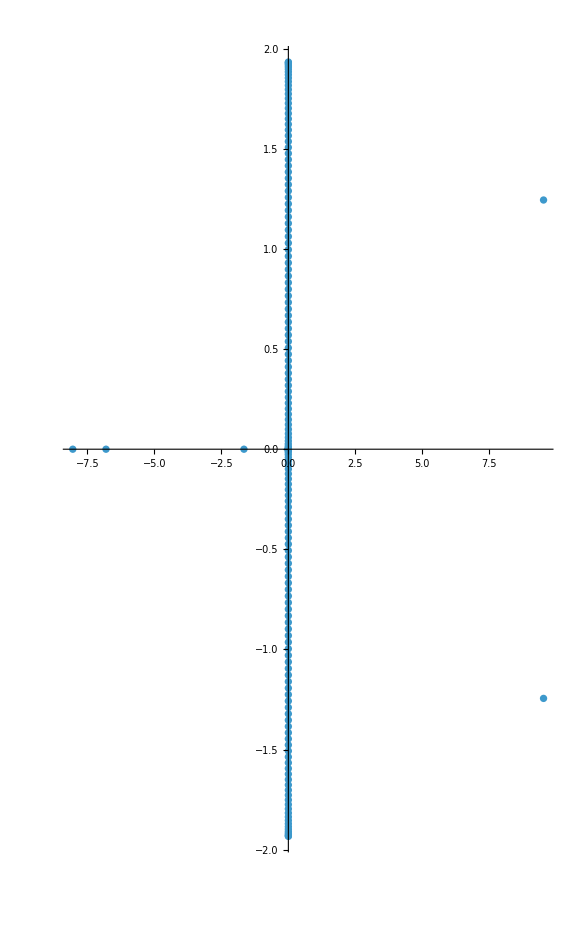

```mathematica
singleEigenvalueTest [κcVal_,ϵVal_,σ_]:= Module[{αval,βval,a0val,a1val,a2val,a3val,γ00val, γ01val,γ02val,γ10val,γ11val,γ12val,γ13val,γ20val,γ21val,γ22val, γ23val,γ24val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a20val,a21val,a22val,a23val,a24val,a25val,a26val, interior, boundary, coeff,LHSBars,RHSBars1,RHSBars2, barCoeffs, LHSNum, RHSNum, mat, eigs},
Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs0.mx"];
Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs1.mx"];
Get["C:\\Users\\jambl\\OneDrive - Brigham Young University\\Desktop\\Research\\Dr.Hirschmann\\HirschmannGroupBYU\\Notes\\MathematicaNotebooks\\bdCoeffs2.mx"];

γ22val=γ22/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
γ20val=γ20/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
γ21val=γ21/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
γ23val=γ23/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
γ24val=γ24/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a20val=a20/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a21val=a21/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a22val=a22/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a23val=a23/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a24val=a24/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a25val=a25/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
a26val=a26/.coeffs2/.κc->κcVal/.ϵ->ϵVal;
(* a26val=a26/.{coeffs2/.(Join[interiorCoeffs,{yHat->yHat2List[[xx]]}])}/.{yHat->yHat2List[[xx]]}; *)



γ11val=γ11/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
γ10val=γ10/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
γ12val=γ12/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
γ13val=γ13/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a10val=a10/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a11val=a11/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a12val=a12/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a13val=a13/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a14val=a14/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a15val=a15/.coeffs1/.κc->κcVal/.ϵ->ϵVal;
a16val=a16/.coeffs1/.κc->κcVal/.ϵ->ϵVal;



γ00val=γ00/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
γ01val=γ01/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
γ02val=γ02/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a00val=a00/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a01val=a01/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a02val=a02/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a03val=a03/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a04val=a04/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a05val=a05/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
a06val=a06/.coeffs0/.κc->κcVal/.ϵ->ϵVal;
(*γ00val=γ00val/γ00val/.{yHat->yHat0List[[zz]]};*)

αval = α/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
βval=β/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
a1val=a1/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
a2val=a2/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
a3val=a3/.interiorCoeffs /.κc->κcVal/.ϵ->ϵVal;
a0val=-2(a1val+a2val+a3val);

interior={α->αval,β->βval,a0->a0val,a1->a1val,a2->a2val,a3->a3val};
boundary={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeff=Flatten[Join[interior,boundary]];

(*Print[coeff];*)

LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeff),
γ13Bar->(γ13/(1-γ10*γ01)/.coeff),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeff),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeff),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeff)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeff;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeff;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];


LHSNum=(LHS[k]/.coeff)/.barCoeffs;
RHSNum=(RHS[k]/.coeff)/.barCoeffs;
Print[LHSNum//MatrixForm];
Print[RHSNum//MatrixForm];

mat=Inverse[P].Q.(IdentityMatrix[k]+σ Inverse[LHSNum].RHSNum);
eigs=-Eigenvalues[mat];

(*Print[eigs];*)
ComplexListPlot[eigs,AspectRatio->GoldenRatio,PlotRange->All,ImageSize->Large]
]

singleEigenvalueTest [0.8π,0,1]
```